# K_0 NDF

This is code to accompany the book:
A Hitchhiker’s Guide to Multiple Scattering
© 2020 Eugene d’Eon 
www.eugenedeon.com/hitchhikers

### notation

u = m . n = Cos[θ_m]
α  = roughness

## Definitions and derivations

```mathematica
K0`D[u_,α_]:=(2 BesselK[0,(2 √(1-u^2))/(u α)])/(π u^4 α^2)HeavisideTheta[u]
```

```mathematica
K0`σ[u_,α_]:=u (1+(ⅇ^(-(2 u)/(√(1-u^2) α)) √(1-u^2) α)/(4 u))HeavisideTheta[u]+HeavisideTheta[-u] 1/4 ⅇ^((2 u)/(√(1-u^2) α)) √(1-u^2) α
```

```mathematica
K0`Λ[u_,α_]:=(ⅇ^(-(2 u)/(√(1-u^2) α)) √(1-u^2) α)/(4 u)
```

```mathematica
FullSimplify[K0`Λ[u,u/(√(1-u^2) x)],Assumptions->0<u<1&&x>0]
```

ⅇ^(-2 x)/(4 x)

### derivation

```mathematica
Beckmann`D[u_,α_]:=(ⅇ^(-(-1+1/u^2)/α^2))/(α^2 π u^4)HeavisideTheta[u]
```

```mathematica
Integrate[Beckmann`D[u,α √m]Exp[-m],{m,0,Infinity},Assumptions->0<u<1&&α>0]
```

(2 BesselK[0,(2 √(1-u^2))/(u α)])/(π u^4 α^2)

General::munfl: Exp[-9.58482×10^9] is too small to represent as a normalized machine number; precision may be lost.

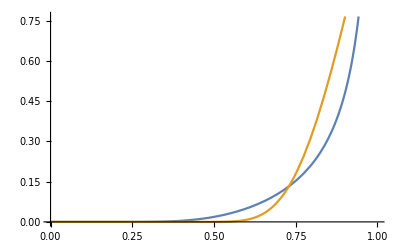

```mathematica
Plot[{K0`D[u,m],Beckmann`D[u,m]}/.m->.5//Evaluate,{u,0,1}]
```

The NDF is singular at u = 1.

```mathematica
Limit[K0`D[u,a],u->1,Assumptions->a>0,Direction->"FromBelow"]
```

∞

### shape invariant f(x)

```mathematica
FullSimplify[K0`D[u,α] u^4 α^2/.u->1/(√(1+x^2 α^2)),Assumptions->1-1/(√(1+x^2 α^2))>0&&x>0&&α>0]
```

(2 BesselK[0,2 x])/π

### height field normalization

```mathematica
NIntegrate[2Pi u K0`D[u,.6],{u,0,1}]
```

1.

### distribution of slopes

```mathematica
FullSimplify[K0`D[1/(√(p^2+q^2+1)),α](1/(√(p^2+q^2+1)))^4,Assumptions->0<α<1&&p>0&&q>0]
```

(2 BesselK[0,(2 √(p^2+q^2))/α])/(π α^2)

```mathematica
K0`P22[p_,q_,α_]:=(2 BesselK[0,(2 √(p^2+q^2))/α])/(π α^2)
```

```mathematica
Integrate[K0`P22[p,q,α],{p,-Infinity,Infinity},{q,-Infinity,Infinity},Assumptions->0<α<1]
```

1

### compare σ to delta integral:

```mathematica
Delta`σ[u_,ui_]:=Re[2(√(1-u^2-ui^2)+u ui ArcCos[-(u ui)/(√(1-u^2) √(1-ui^2))])]
```

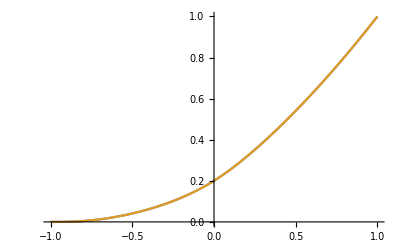

```mathematica
With[{α=.8},
Plot[{
Quiet[NIntegrate[K0`D[ui,α]Delta`σ[u,ui],{ui,0,1}]],
Quiet[K0`σ[u,α]]
},{u,-1,1}]
]
```